```mathematica
(*

Decaying damping.

η = γ Log[t+1]

*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{q'[t]==(t+1)^-γ p[t], p'[t]==-(t+1)^γ q[t],q[0]==a,p[0]==0},{q[t],p[t]},t]//FullSimplify
```

{{p[t]→1/2 a π (1+t)^((1+γ)/2) (BesselJ[(1+γ)/2,1+t] BesselY[(1+γ)/2,1]-BesselJ[(1+γ)/2,1] BesselY[(1+γ)/2,1+t]),q[t]→1/2 a π (1+t)^(1/2-γ/2) (BesselJ[(1+γ)/2,1] BesselY[1/2 (-1+γ),1+t]-BesselJ[1/2 (-1+γ),1+t] BesselY[(1+γ)/2,1])}}

```mathematica
pos[t_,γ_,q0_]:=1/2 q0 π (1+t)^(1/2-γ/2) (BesselJ[(1+γ)/2,1] BesselY[1/2 (-1+γ),1+t]-BesselJ[1/2 (-1+γ),1+t] BesselY[(1+γ)/2,1])
mom[t_,γ_,q0_]:=1/2 q0 π (1+t)^((1+γ)/2) (BesselJ[(1+γ)/2,1+t] BesselY[(1+γ)/2,1]-BesselJ[(1+γ)/2,1] BesselY[(1+γ)/2,1+t])
ham[q_,p_,t_,γ_]:=(1/2)(1+t)^-γ p^2 + (t+1)^γ q^2/2
```

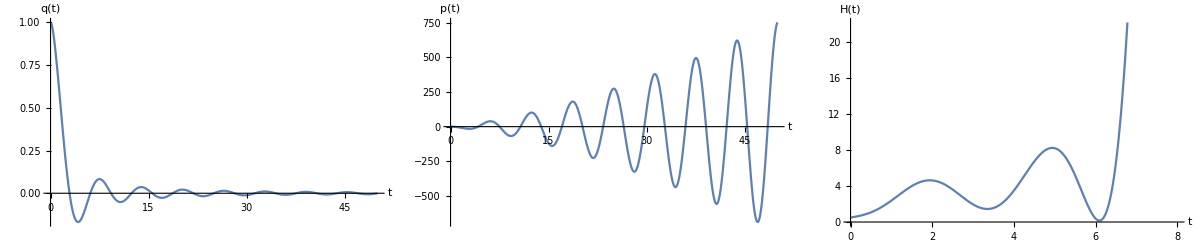

```mathematica
γ=3.;
T=50.;
q0=1;
g=GraphicsRow[{
Plot[pos[t,γ,q0], {t,0,T},PlotRange->Full,
AxesLabel->{Style[HoldForm[t],12],Style[HoldForm[q[t]],12]}],
Plot[mom[t,γ,q0], {t,0,T},PlotRange->Full,
AxesLabel->{Style[HoldForm[t],12],Style[HoldForm[p[t]],12]}],
Plot[ham[pos[t,γ,q0],mom[t,γ,q0],γ,t], {t,0,8},PlotRange->Automatic,
AxesLabel->{Style[HoldForm[t],12],Style[HoldForm[H[t]],12]},PlotRangePadding->{.0,.0}]
},Spacings->{0,0}]
```

```mathematica
Export["/Users/gui/my_papers/dissipative_symplectic/arxiv/quad_dec.pdf",g]
```

/Users/gui/my_papers/dissipative_symplectic/arxiv/quad_dec.pdf

```mathematica
Nesterov[q0_,γ_,T_,MaxIter_]:=(
h=T/MaxIter;
t=0;
q=q0;
p=0;
data={};
For[k=1,k<=MaxIter,k++,

μ=(t+1)^-γ;
oldq=q;
q=q+h μ p;
g=q;
p=μ p-h g;
q=oldq+h p;
t=t+h;
numham=H[q,p (t+1)^γ,t,γ];

trueham=H[Q[t,γ,q0],P[t,γ,q0],t,γ];
AppendTo[data,{t,Abs[trueham-numham]}];

];

Return[data];
)

Euler1[q0_,γ_,maxT_,maxiter_]:=(

h=maxT/maxiter;
t=0;
q=q0;
p=0;

data={};
For[k=1,k≤maxiter,k++,

g=q;
p=p-h (t+1)^γ g;
q=q+h (t+1)^-γ p;
t=t+h;
numham=ham[q,p,t,γ];

trueham=ham[pos[t,γ,q0],mom[t,γ,q0],t,γ];
AppendTo[data,{t,Abs[trueham-numham]}];

];

Return[data];

)

Leapfrog1[q0_,γ_,maxT_,maxiter_]:=(

h=maxT/maxiter;
t=0;
q=q0;
p=0;

data={};
For[k=1,k≤maxiter,k++,

g=q;
p=p-(h/2) (t+1)^γ g;
t=t+h;
q=q+(h/2)((t+1-h)^-γ+(t+1)^-γ) p;
g=q;
p=p-(h/2) (t+1)^γ g;
numham=ham[q,p,t,γ];

trueham=ham[pos[t,γ,q0],mom[t,γ,q0],t,γ];
AppendTo[data,{t,Abs[trueham-numham]}];

];

Return[data];

)

Yoshida1[q0_,γ_,maxT_,maxiter_]:=(

ϵ=maxT/maxiter ;
t=0;
q=q0;
p=0;

data={};
κ=2^(1/3)//N;
For[k=1,k≤maxiter,k++,

a=1./(2.-κ);
h=a*ϵ;
g=q;
p=p-(h/2) (t+1)^γ g;
t=t+h;
q=q+(h/2)((t+1-h)^-γ+(t+1)^-γ) p;
g=q;
p=p-(h/2) (t+1)^γ g;


b=-κ/(2.-κ);
h=b*ϵ;
g=q;
p=p-(h/2) (t+1)^γ g;
t=t+h;
q=q+(h/2)((t+1-h)^-γ+(t+1)^-γ) p;
g=q;
p=p-(h/2) (t+1)^γ g;

a=1./(2.-κ);
h=a*ϵ;
g=q;
p=p-(h/2) (t+1)^γ g;
t=t+h;
q=q+(h/2)((t+1-h)^-γ+(t+1)^-γ) p;
g=q;
p=p-(h/2) (t+1)^γ g;

numham=ham[q,p,t,γ];

trueham=ham[pos[t,γ,q0],mom[t,γ,q0],t,γ];
AppendTo[data,{t,Abs[trueham-numham]}];

];

Return[data];

)
```

```mathematica
dataEu=Euler1[1.,3.,50.,10000];
dataLf=Leapfrog1[1.,3.,50.,10000];
dataYo=Yoshida1[1.,3.,50.,10000];
```

```mathematica
dataYo;
```

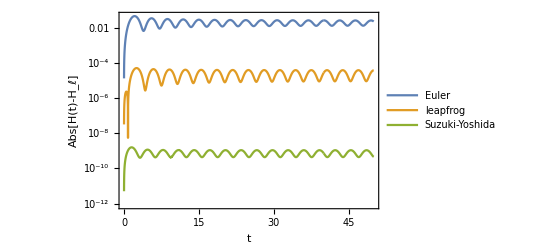

```mathematica
dataEu2 = Take[dataEu,{1,-1,1}];
dataLf2 = Take[dataLf,{1,-1,1}];
dataYo2=Take[dataYo,{1,-1,1}];
g=ListLogPlot[{
dataEu2[[All,{1,2}]],
dataLf2[[All,{1,2}]],
dataYo2[[All,{1,2}]]},
Joined->True,
Frame->True, 
FrameLabel->{Style[HoldForm[t],FontSize->14],Style[HoldForm[Abs[H[t] - Subscript[H, ℓ]] ],FontSize->14]},PlotLegends->Placed[{"Euler", "leapfrog", "Suzuki-Yoshida"},Top]]
```

```mathematica
Export["/Users/gui/my_papers/dissipative_symplectic/arxiv/quad_dec_ham.pdf",g]
```

/Users/gui/my_papers/dissipative_symplectic/arxiv/quad_dec_ham.pdf

```mathematica
dataLf=Leapfrog1[1.,-1,10,1000];
dataNe=Nesterov[1.,-0.01,10,1000];
```

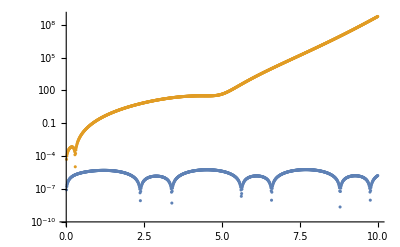

```mathematica
ListLogPlot[{dataLf,dataNe}]
```